# Metastable states?

### Parallel lines code

Let’s do two parallel lines. 
    M= total number of sites. 
    L= sites per layer = M/2.
    H1 = Hamiltonian for first layer.
    H2 = Hamiltonian for second layer.
    H12 = Hamiltonian between layers.
    Hp = Hamiltonian for parallel layers
    InterLayerCoupling = coupling strength between lines

```mathematica
Id={{1,0},{0,1}};
Sx=(1/2) {{0,1},{1,0}};
Sy=(1/2) {{0,-I},{I,0}};
Sz=(1/2) {{1,0},{0,-1}};
h=KroneckerProduct[Sx,Sx]+KroneckerProduct[Sy,Sy]+KroneckerProduct[Sz,Sz]-1/4 KroneckerProduct[Id,Id];
(*The function hRand[s] creates a random local XXZ operator between two sites where the anisotropry paramater Delta is normally distributed with mean 1 and standard deviation 1*)
hRand[σ_]:=KroneckerProduct[Sx,Sx]+KroneckerProduct[Sy,Sy]+RandomVariate[NormalDistribution[1,σ]] (KroneckerProduct[Sz,Sz]-1/4 KroneckerProduct[Id,Id]);
vec[x_,L_]:=Table[If[EvenQ[Floor[k/2^(L-x)]],1,0],{k,0,2^L-1}]
(*The functions "OnePtBottom" and "OnePtTop" compute the 1-point functions for the Bottom and Top lines, respectively, for a collection of states evs.*)
OnePtBottom[k_,evs_,M_,L_,keepIndices_]:=Module[{Evec,norm,table,j},Evec=evs[[k]]//N;
norm=Norm[Evec]^2;
Evec=Map[Function[x,Abs[x]^2],Evec];
table=Table[{j,N[Dot[Evec,vec[j,M][[keepIndices]]]/norm]},{j,1,L}];
Return[table]]
OnePtTop[k_,evs_,M_,L_,keepIndices_]:=Module[{Evec,norm,table,j},Evec=evs[[k]]//N;
norm=Norm[Evec]^2;
Evec=Map[Function[x,Abs[x]^2],Evec];
table=Table[{j,N[Dot[Evec,vec[L+j,M][[keepIndices]]]/norm]},{j,1,L}];
Return[table]]
(*REMARK:I've changed the "ParallelLines" function to add an inhomogeneous magnetic field B with max stength b and random XXZ anisotropy parameters Δ with Normal distributions centered at 1 and with standard deviation σ.*)
ParallelLines[M_,L_,InterLayerCoupling_, b_, σ_]:=Module[{H1,H2,H12, B,basis,keepIndices,Hp,trimmedHp},
B= Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], ((L-k)/(L-1))b Sz, IdentityMatrix[2^(M-k)]], {k, 1, L}] +Sum[KroneckerProduct[IdentityMatrix[2^(L-1+k)], (1/2)((L-k)/(L-1))b Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}];
H1 =  Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], hRand[σ], IdentityMatrix[2^(M-k-1)]], {k, 1, L-1}] ;
H2 = Sum[KroneckerProduct[IdentityMatrix[2^(L +k-1)], hRand[σ], IdentityMatrix[2^(L-k-1)]], {k, 1, L-1}];
H12 = Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sx, IdentityMatrix[2^(L-1)], Sx, IdentityMatrix[2^(L-k)]], {k, 1, L}]+Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sy, IdentityMatrix[2^(L-1)], Sy, IdentityMatrix[2^(L-k)]], {k, 1, L}]+ (Sum[KroneckerProduct[IdentityMatrix[2^(k-1)], Sz, IdentityMatrix[2^(L-1)], Sz, IdentityMatrix[2^(L-k)]], {k, 1, L}] - (L/4)IdentityMatrix[2^M]);
Hp = -H1 - H2 + (InterLayerCoupling*H12) + B;

basis = Table[IntegerDigits[2^M-k, 2,M], {k ,1, 2^M}];
(* We consider the case where half the spins are flipped. I.e. ferromagnetic within the layer, antiferromagnetic between layers. Ultimately, we want to evolve the state where one spin in each layer is flipped *)
keepIndices = Flatten[Position[basis,x_/;Count[x,0]==L]];
trimmedHp = Hp[[keepIndices,keepIndices]];
Return[{trimmedHp, keepIndices}]
]
WaveFunction[Eigenvalues_,Eigenvectors_,ConfigurationIndex_,t_,hbar_]:=Sum[Eigenvectors[[k]][[ConfigurationIndex]]*Exp[-I*Eigenvalues[[k]]*t/hbar]*Eigenvectors[[k]],{k,1,Length[Eigenvectors]}]
```

### Parallel line code: L=3, J_intra=1/10

```mathematica
L=3;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0, 1/1000];
MatrixForm[Hp]
keepIndices

(*ListPlot[Eigenvalues[H]]*)
```

(-0.15 | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0.948885 | -0.5 | 0. | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 1.44904 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0. | -0.5 | 0.849828 | 0. | 0. | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 0. | 0. | 1.4483 | -0.5 | 0. | 0. | 0.05 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0.05 | 0. | -0.5 | 0. | -0.5 | 1.84845 | -0.5 | 0. | 0. | 0.05 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.44924 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0.
0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0.94957 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 1.44879 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | -0.5 | 0.848627 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0.05
0.05 | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.848627 | -0.5 | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.44879 | -0.5 | 0. | 0. | 0.05 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0.94957 | 0. | 0. | 0. | 0. | 0. | 0.05 | 0.
0. | 0. | 0.05 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 1.44924 | -0.5 | 0. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.05 | 0. | 0. | -0.5 | 1.84845 | -0.5 | 0. | -0.5 | 0. | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0.05 | 0. | 0. | -0.5 | 1.4483 | 0. | 0. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 0. | 0. | 0.849828 | -0.5 | 0. | 0.05
0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.44904 | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | -0.5 | 0. | -0.5 | 0.948885 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.05 | 0. | 0. | 0. | 0. | 0.05 | 0. | 0.05 | 0. | 0. | -0.15)

{8,12,14,15,20,22,23,26,27,29,36,38,39,42,43,45,50,51,53,57}

```mathematica
Eigs = Eigenvalues[Hp];
```

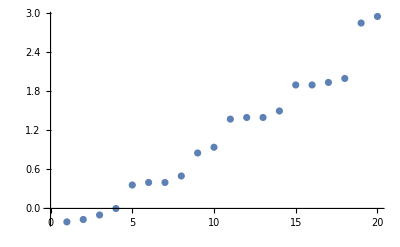

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

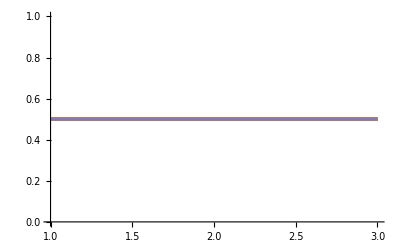

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,M,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

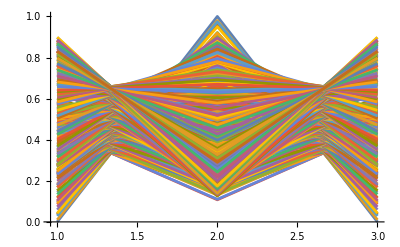

```mathematica
ListPlot[OnePtWave, Joined->True]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

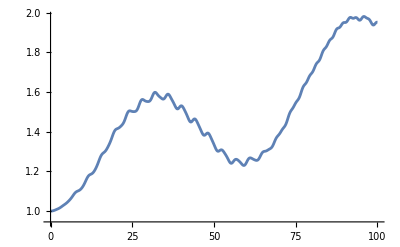

```mathematica
(*A plot of the expected number of up-spins on the top layer as a function of time. Let's think about this plot and make sure that it makes sense*)
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

### Parallel line code: L=3, J_intra=0

```mathematica
L=3;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,0,0, 1/1000];
MatrixForm[Hp]
keepIndices

(*ListPlot[Eigenvalues[H]]*)
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 1.00008 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 1.50015 | -0.5 | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 1.00004 | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -0.5 | 0. | 0. | 1.50042 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | -0.5 | 0. | -0.5 | 2.00049 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.50038 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 1.00041 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 1.50052 | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 1.00045 | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 1.00045 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.50052 | -0.5 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.00041 | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | 0. | 1.50038 | -0.5 | 0. | -0.5 | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 2.00049 | -0.5 | 0. | -0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 0. | 0. | -0.5 | 1.50042 | 0. | 0. | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | 0. | 1.00004 | -0.5 | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.50015 | -0.5 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -0.5 | 0. | -0.5 | 1.00008 | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

{8,12,14,15,20,22,23,26,27,29,36,38,39,42,43,45,50,51,53,57}

```mathematica
Eigs = Eigenvalues[Hp];
```

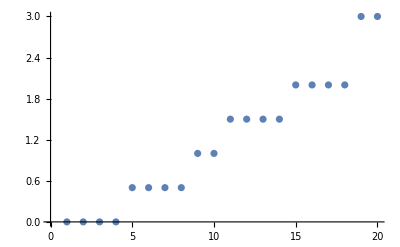

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

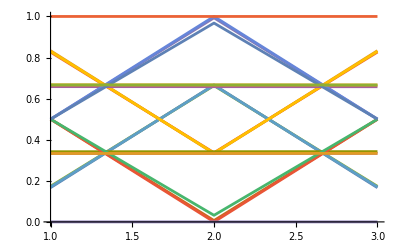

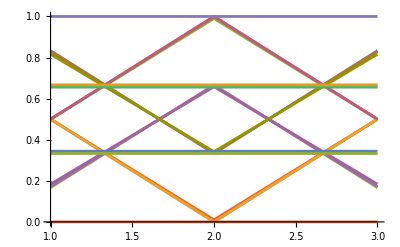

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,M,t,1]],{t,0,10,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

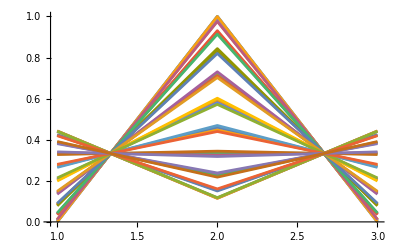

```mathematica
ListPlot[OnePtWave, Joined->True]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

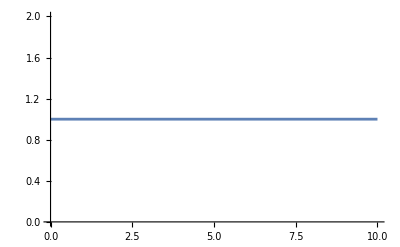

```mathematica
ListPlot[Table[{(t-1)*0.2,Sum[OnePtWave[[t]][[k]][[2]],{k,1,L}]},{t,1,Length[OnePtWave]}],Joined->True]
```

### Parallel line code: L=4, J_intra=1/10

```mathematica
L=4;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0, 1/1000];
keepIndices
(*ListPlot[Eigenvalues[H]]*)
```

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241}

```mathematica
Eigs = Eigenvalues[Hp];
```

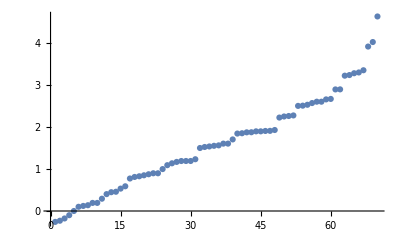

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

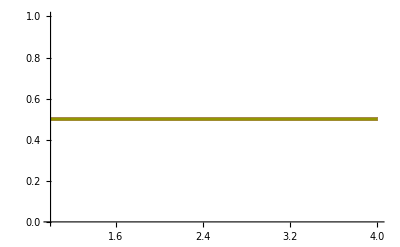

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,8,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
OnePtWave2=Table[OnePtBottom[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
(*The following operation keeps track of the down-spin the bottom layer instead of the up-spin.*)
inv =Table[{0, 1}, {k,1,L}] ;
OnePtWave2=Map[Function[x,Abs[inv-x]],OnePtWave2];
```

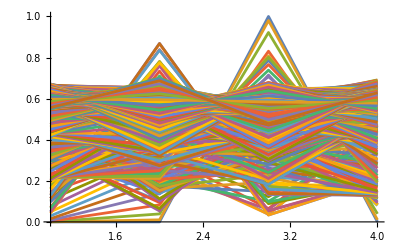

```mathematica
ListPlot[OnePtWave, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
Animate[ListPlot[ OnePtWave2[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

```mathematica
(*Plots of the one-point functions for the top and a bottom layer. The plots seem to match well through time.*)
Animate[ListPlot[ {OnePtWave[[t]],OnePtWave2[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

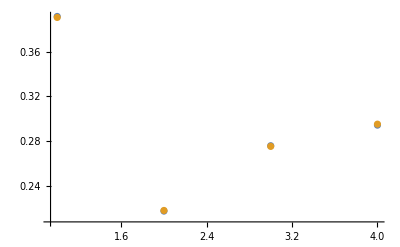

{{1,0.391526},{2,0.217582},{3,0.275967},{4,0.294397}}

{{1,0.390637},{2,0.218141},{3,0.275415},{4,0.29528}}

```mathematica
ListPlot[{OnePtWave[[50]],OnePtWave2[[50]]}]
OnePtWave[[50]]
OnePtWave2[[50]]
```

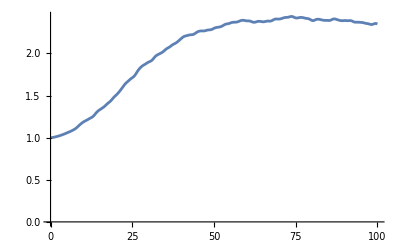

```mathematica
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

### Parallel line code: L=4, J_intra=0

```mathematica
L=4;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,0,0, 1/1000];
keepIndices
(*ListPlot[Eigenvalues[H]]*)
```

{16,24,28,30,31,40,44,46,47,52,54,55,58,59,61,72,76,78,79,84,86,87,90,91,93,100,102,103,106,107,109,114,115,117,121,136,140,142,143,148,150,151,154,155,157,164,166,167,170,171,173,178,179,181,185,196,198,199,202,203,205,210,211,213,217,226,227,229,233,241}

```mathematica
Eigs = Eigenvalues[Hp];
```

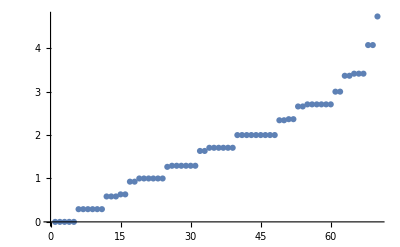

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

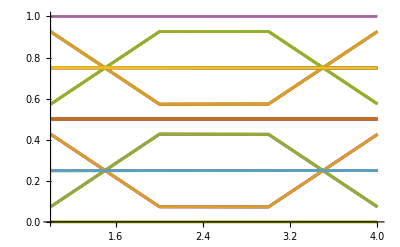

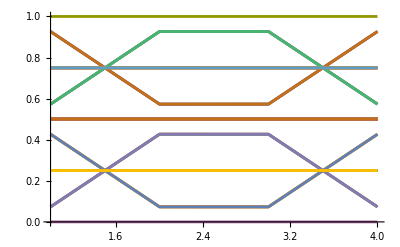

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecsUC = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
EvaluationUC = Table[Chop[WaveFunction[Eigs,NEVecsUC ,8,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWaveUC=Table[OnePtTop[k,EvaluationUC,M,L,keepIndices],{k,1,Length[EvaluationUC]}];
```

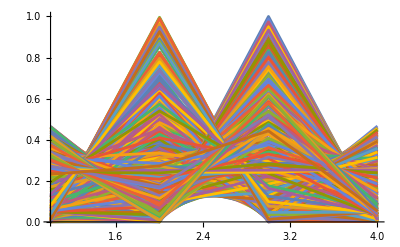

```mathematica
ListPlot[OnePtWaveUC, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
Animate[ListPlot[OnePtWaveUC[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
Animate[ListPlot[ {OnePtWave[[t]],OnePtWaveUC[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
ListPlot[{OnePtWave[[50]],OnePtWave2[[50]]}]
OnePtWave[[50]]
OnePtWave2[[50]]
```

-Graphics-

{{1,0.391526},{2,0.217582},{3,0.275967},{4,0.294397}}

{{1,0.390637},{2,0.218141},{3,0.275415},{4,0.29528}}

```mathematica
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```

-Graphics-

### Parallel line code: L=5, J_intra=1/10

```mathematica
L=5;
M=2L;
{Hp, keepIndices} = ParallelLines[M,L,1/10,0, 1/1000];
keepIndices
(*ListPlot[Eigenvalues[H]]*)
```

{32,48,56,60,62,63,80,88,92,94,95,104,108,110,111,116,118,119,122,123,125,144,152,156,158,159,168,172,174,175,180,182,183,186,187,189,200,204,206,207,212,214,215,218,219,221,228,230,231,234,235,237,242,243,245,249,272,280,284,286,287,296,300,302,303,308,310,311,314,315,317,328,332,334,335,340,342,343,346,347,349,356,358,359,362,363,365,370,371,373,377,392,396,398,399,404,406,407,410,411,413,420,422,423,426,427,429,434,435,437,441,452,454,455,458,459,461,466,467,469,473,482,483,485,489,497,528,536,540,542,543,552,556,558,559,564,566,567,570,571,573,584,588,590,591,596,598,599,602,603,605,612,614,615,618,619,621,626,627,629,633,648,652,654,655,660,662,663,666,667,669,676,678,679,682,683,685,690,691,693,697,708,710,711,714,715,717,722,723,725,729,738,739,741,745,753,776,780,782,783,788,790,791,794,795,797,804,806,807,810,811,813,818,819,821,825,836,838,839,842,843,845,850,851,853,857,866,867,869,873,881,900,902,903,906,907,909,914,915,917,921,930,931,933,937,945,962,963,965,969,977,993}

```mathematica
Eigs = Eigenvalues[Hp];
```

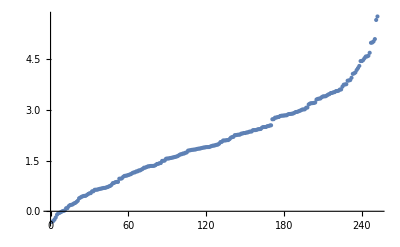

```mathematica
ListPlot[Sort[Eigs, Less]]
```

```mathematica
EVs = Eigenvectors[Hp];
```

```mathematica
OPB = Table[OnePtBottom[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
OPT = Table[OnePtTop[k, EVs, M,L, keepIndices], {k,1, Length[EVs]}];
```

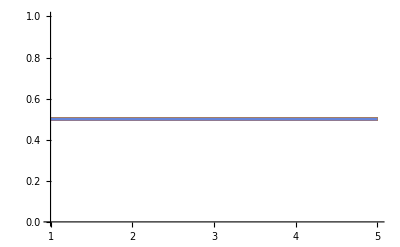

-Graphics-

```mathematica
ListPlot[OPB,Joined->True,PlotRange->{{1,L},{0,1}}]
ListPlot[OPT,Joined->True,PlotRange->{{1,L},{0,1}} ]
```

```mathematica
NEVecs = Map[Function[x, x/Norm[x]], EVs];
```

```mathematica
Evaluation = Table[Chop[WaveFunction[Eigs,NEVecs ,24,t,1]],{t,0,100,0.2}];
```

```mathematica
OnePtWave=Table[OnePtTop[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
OnePtWave2=Table[OnePtBottom[k,Evaluation,M,L,keepIndices],{k,1,Length[Evaluation]}];
```

```mathematica
inv =Table[{0, 1}, {k,1,L}] ;
OnePtWave2=Map[Function[x,Abs[inv-x]],OnePtWave2];
```

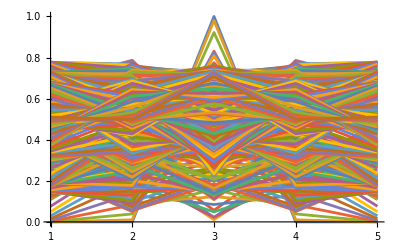

```mathematica
ListPlot[OnePtWave, Joined->True, PlotRange->{{1, L}, {0,1}}]
```

```mathematica
Animate[ListPlot[OnePtWave[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave], 1}]
```

```mathematica
Animate[ListPlot[ OnePtWave2[[t]], Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

```mathematica
Animate[ListPlot[ {OnePtWave[[t]],OnePtWave2[[t]]}, Joined->True, PlotRange->{{1,L}, {0,1}}], {t, 1, Length[OnePtWave2], 1}]
```

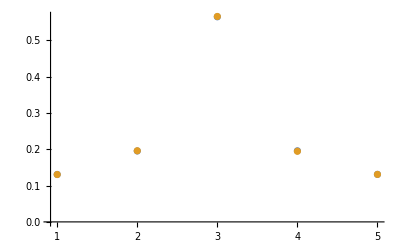

{{1,0.130675},{2,0.195429},{3,0.565189},{4,0.195883},{5,0.130913}}

{{1,0.130553},{2,0.196033},{3,0.566102},{4,0.194526},{5,0.130875}}

```mathematica
ListPlot[{OnePtWave[[50]],OnePtWave2[[50]]}]
OnePtWave[[50]]
OnePtWave2[[50]]
```

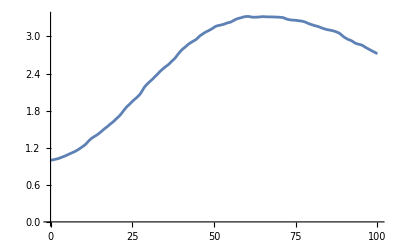

```mathematica
ListPlot[Table[{(t-1)*0.2, Sum[OnePtWave[[t]][[k]][[2]], {k, 1, L}]},{t, 1, Length[OnePtWave]} ], Joined->True]
```